# OptPacking Algorithm - NMinimize

## Geometrical Definitions

### Definitions

```mathematica
regpolypts[n_Integer,d_]:=d/Cos[π/n] Table[AngleVector[θ+π/n-π/2],{θ,0,2(π-1/n),2 π/n}]
```

```mathematica
border[pts_List]:=Line @ Join[pts,{pts⟦1⟧}]
```

### Testing

```mathematica
trianglepts=regpolypts[3, 1];
```

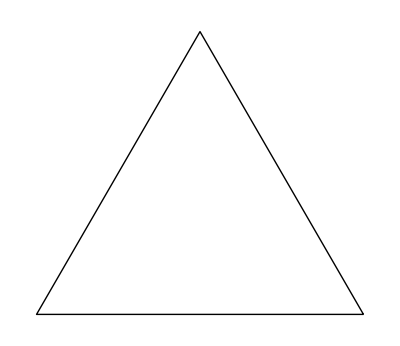

```mathematica
Graphics[border[trianglepts]]
```

## Constraints

### overlapC

#### Definition

Table of circle overlap constraints, flattened.

```mathematica
overlapC[radii_List, circlevars_List]:=Table[
(radii⟦i⟧+radii⟦j⟧)^2≤ (circlevars⟦i⟧-circlevars⟦j⟧).(circlevars⟦i⟧-circlevars⟦j⟧),
{i, circlevars//Length}, {j, i+1, circlevars//Length}
]//Flatten
```

#### testing

```mathematica
Clear[r, a, b, c, d, e, f, vars];
```

```mathematica
r={1,1,2};
vars={{a, b}, {c, d}, {e, f}};
```

```mathematica
overlapC[r, vars]
```

{4≤(a-c)^2+(b-d)^2,9≤(a-e)^2+(b-f)^2,9≤(c-e)^2+(d-f)^2}

### distanceQ

#### Definition

Checks if circle is within radius of border, on inner side. Points need to be in counterclockwise order. Normal vector pointed left.

```mathematica
distanceQ[{bp1:{a_, b_}, bp2:{c_,d_}}, {xc_, yc_}, r_]:=(r ((d-b)^2+(c-a)^2)^.5+(d-b)xc-(c-a)yc≤ a d-c b)
(*True if circle doesn't overlap border on LHS*)
```

#### testing

```mathematica
bp1={1,2};
bp2={0,2};
cp={.5, 1.6};
r=.1;
```

```mathematica
distanceQ[{bp1, bp2}, cp, r]
```

True

### borderC

#### Definition

Table of border constraints

```mathematica
borderC[radii_List, circlevars_List, polygon_List]:=Block[{pnumber=polygon//Length, cnumber=radii//Length, borderlines},
borderlines=Join[polygon, {polygon⟦1⟧}]//Partition[#, 2,1]&;
Table[distanceQ[borderlines⟦j⟧, circlevars⟦i⟧, radii⟦i⟧], {i, cnumber},{j, pnumber}]//Flatten
]
```

#### testing

```mathematica
Clear[tri, r, circlevars, x, y]
```

```mathematica
tri=regpolypts[3, d];
r={1,1};
circlevars={{a, b}, {c, e}};
```

```mathematica
borderC[r, circlevars, tri]
```

{3 a d+√3 b d+2 √3 Abs[d]≤2 √3 d^2,-3 a d+√3 b d+2 √3 Abs[d]≤2 √3 d^2,-2 √3 b d+2 √3 Abs[d]≤2 √3 d^2,3 c d+√3 d e+2 √3 Abs[d]≤2 √3 d^2,-3 c d+√3 d e+2 √3 Abs[d]≤2 √3 d^2,-2 √3 d e+2 √3 Abs[d]≤2 √3 d^2}

## Optimization Algorithm

Fixed radii, optimal polygon packing algorithm.

### varMat

#### Definition

```mathematica
varMat[circlebound_, circlevars_List, obj_List ]:=Module[
{number=circlevars//Length, boundvec, varM, allvars},
allvars=circlevars//Flatten;
boundvec=Table[circlebound, {2 number}];
varM={allvars, -boundvec, boundvec}//Transpose;
Join[varM, obj]
]
```

#### Testing

```mathematica
Clear[circles, obj]
```

```mathematica
circles={{a, b}, {c, d}};
obj={{e, 0, 5}};
```

```mathematica
varMat[5, circles, obj]//MatrixForm
```

(a | -5 | 5
b | -5 | 5
c | -5 | 5
d | -5 | 5
e | 0 | 5)

### optPacking

#### Definition

```mathematica
optPacking[radii_List, polygon_, objective_, objbound_List, positionbound_, opts___]:=
Module[
{number = radii//Length, circlevars, x, y,varMatwb, constraints, overlapcons, bordercons, Sol, filtered },
circlevars=Table[{ToExpression["x"<>ToString[i]], ToExpression["y"<>ToString[i]]},{i, number}];

(*defining constraints*)
overlapcons=overlapC[radii, circlevars];
bordercons=borderC[radii, circlevars, polygon];
constraints=Join[overlapcons, bordercons];

(*variable matrix with index bound and objective bound*)
varMatwb=varMat[positionbound, circlevars, objbound];

(*method call*)
Sol= NMinimize[{objective, constraints}, varMatwb, Method->"SimulatedAnnealing"];

(*filter data*)
filtered=(Sol⟦2⟧/.Rule->List)⟦All, 2⟧;

(*returns list of coordinate tuples, and optimal d*)
{filtered//Partition[#, 2]&, filtered⟦-1⟧}

]
```

#### testing

```mathematica
Clear[d]
epts = regpolypts[3,d];
```

```mathematica
data=optPacking[{1,1,.2, .4, .8, .9}, epts, d, {{d, 0, 8}}, 8]
```

{{{1.27344,-0.865516},{-0.308863,0.357729},{-1.65846,0.426076},{2.53835,-1.46552},{-7.58699×10^-10,2.13103},{-1.67232,-0.965516}},1.86552}

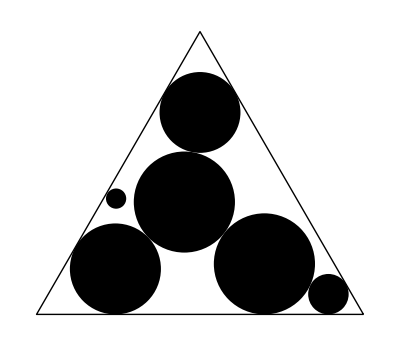

```mathematica
optPlot[{1,1,.2, .4, .8, .9}, epts/.d->data⟦-1⟧, data⟦1⟧]
```

## Visualization

### optPlot

#### Definition

```mathematica
optPlot[radii_List, polygon_List, circlevars_List]:=Module[{number=radii//Length},
Show[Graphics@border[polygon],
Graphics@Table[{Disk[circlevars⟦i⟧, radii⟦i⟧]}, {i, number}]]]
```

#### testing

```mathematica
Clear[r, polygon, circlevars]
```

```mathematica
r={1,1.5,.5};
polygon=regpolypts[3, 3];
circlevars={{1,1},{-2,-2},{-2, 1}};
```

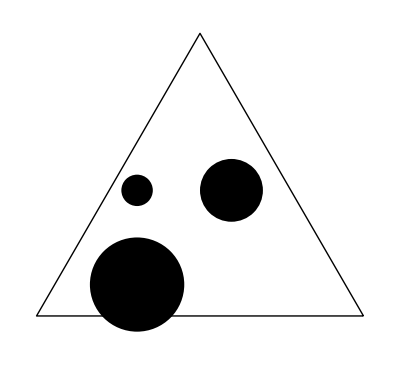

```mathematica
optPlot[r, polygon, circlevars]
```

## Tests

#### test1

```mathematica
Clear[data, tri, rset1]
```

```mathematica
rset1=Join[Table[1,{10}], Table[.5, {5}]];
tri=regpolypts[3, d]
```

{{√3 d,-d},{0,2 d},{-√3 d,-d}}

```mathematica
data=optPacking[rset1, tri, d, {{d, 0,15}}, 15]
```

NMinimize::incst: NMinimize was unable to generate any initial points satisfying the inequality constraints …. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

{{{2.00001,1.30698},{-0.626173,-2.38484},{4.13189,-2.38555},{-4.13189,-2.38554},{-2.90717,-0.768494},{2.37944,-0.656697},{-0.0000132962,4.77107},{-0.739294,1.92998},{1.37391,-2.38555},{0.999969,3.03901},{-1.55808,0.173723},{3.85777,-0.910781},{-2.53802,1.37511},{-2.66757,-2.83095},{-2.08135,-2.02072}},3.38555}

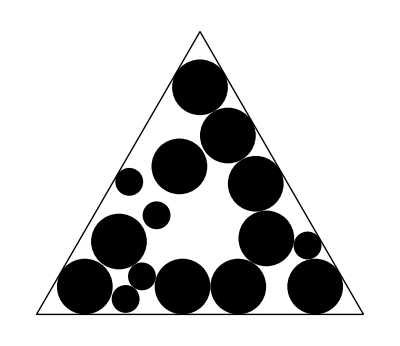

```mathematica
optPlot[rset1, tri/.d->data⟦-1⟧, data⟦1⟧]
```

## Scratch

```mathematica
s={{1,1}, {1,2}}
```

{{1,1},{1,2}}

```mathematica
s⟦1⟧.s⟦2⟧
```

3

```mathematica
{1,1}.{1,2}
```

3

```mathematica
(y2-y1)*xc+(x1-x2)*yc-(x1*y2-x2*y1)
```

x2 y1-x1 y2+xc (-y1+y2)+(x1-x2) yc

```mathematica
-%//Expand
```

-x2 y1+xc y1+x1 y2-xc y2-x1 yc+x2 yc

```mathematica
v={1,2,3}
a={4,5,6}

{v, a}//Transpose//MatrixForm
```

{1,2,3}

{4,5,6}

(1 | 4
2 | 5
3 | 6)

```mathematica
cinp[radii_List,polypts_List,obj_,extravwb_List,circlebnd_,opts___]:=
(**)
Block[
{ncircs = Length[radii],npts = Length[polypts],circvars,x,y,circbnds, circvwb,vwb,cons1,brdr,cons2,cons,res},
circvars = Flatten @ Table[{x[i],y[i]},{i,ncircs}];

circbnds = Table[circlebnd,{2*ncircs}];
circvwb = Transpose[{circvars,-circbnds,circbnds}];
vwb = Join[circvwb,extravwb];
cons1=Flatten [Table[(radii⟦i⟧+radii⟦j⟧)^2 ≤  (x[i]-x[j])^2+(y[i]-y[j])^2,{i,ncircs-1},{j,i+1,ncircs}]];

brdr = Partition[Join[polypts,{polypts⟦1⟧}],2,1];

cons2 = Flatten @ Table[icons[brdr⟦j⟧,{x[i],y[i]},radii⟦i⟧],{i,ncircs},{j,npts}];
cons = Join[cons1,cons2];
res = NMinimize[{obj,cons},vwb,opts];
Print[res⟦{1,3}⟧];
res⟦2⟧
]
```

```mathematica
Table[ToExpression["x"<>ToString@i]]
```

```mathematica
{1,1,12,3,4}//Partition[#, 2]&
```

{{1,1},{12,3}}

```mathematica
test1 = optPacking[{1,1, .5},epts,d,{{d,0,4}},2]
```

{1.57735,{x1→4.38299×10^-8,y1→1.1547,x2→-1.,y2→-0.57735,x3→0.542852,y3→-0.246985,d→1.57735}}

```mathematica
(%[[2]]/.Rule->List)⟦All, 2⟧
```

{4.38299×10^-8,1.1547,-1.,-0.57735,0.542852,-0.246985,1.57735}

```mathematica
test1⟦2⟧/.Rule->List
```

{{x1,4.38299×10^-8},{y1,1.1547},{x2,-1.},{y2,-0.57735},{x3,0.542852},{y3,-0.246985},{d,1.57735}}

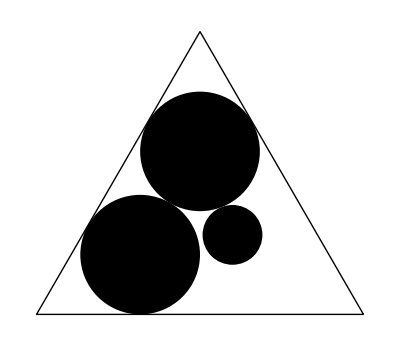

```mathematica
optPlot[{1,1,.5}, epts/.d->1.577, {{0,1.15}, {-1, -.577}, {.543, -.2467}}]
```

```mathematica
{1,1,.2, .4, .8, .9}
```

```mathematica
NMinimize[x^2,{x,0,1},Method->
```

```mathematica
ze[
```